# ESSENTIAL CALCULUS SECOND EDITION JAMES STEWART

## CHAPTER 3 APPLICATIONS OF DIFFERENTIATION

3.1 MAXIMUM AND MINIMUM VALUES

## DEFINITION 1

### -Graphics-

### -Graphics-

## DEFINITION 2

### -Graphics-

### -Graphics--Graphics-

## EXAMPLE 1

### -Graphics-

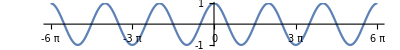

```mathematica
Plot[Cos[x],{x,-6Pi,6Pi},Ticks->{Table[n*Pi,{n,-6,6}],{-1,1}},AspectRatio->1/8]
```

## EXAMPLE 2

### -Graphics--Graphics-

## EXAMPLE 3

### -Graphics--Graphics-

## EXAMPLE 4

### -Graphics-

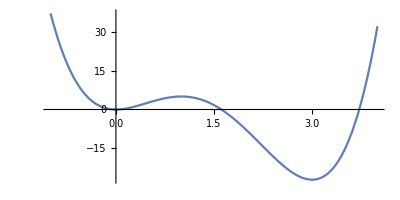

5

37

0

-27

32

```mathematica
Clear[f]
Clear[x]
f[x_]=3 x^4-16 x^3+18 x^2;
Plot[f[x],{x,-1,4},AspectRatio->1/2]
f[1]
f[-1]
f[0]
f[3]
f[4]
```

## THE EXTREME VALUE THEOREM

### -Graphics-

### -Graphics-

### -Graphics-

#### -Graphics--Graphics-

#### -Graphics--Graphics-

## FERMAT’S THEOREM

### -Graphics-

### -Graphics-

### -Graphics-

#### -Graphics- -Graphics--Graphics-

## DEFINITION 6 CRITICAL NUMBER

### -Graphics- -Graphics-

## EXAMPLE 5

### -Graphics-

```mathematica
Clear[f]
Clear[x]
Clear[fPrime]
f[x_]=x^(3/5)(4-x)
fPrime[x_]=Dt[f[x],x]//FullSimplify
Solve[fPrime[x]==0,x]
```

### -Graphics-

## Rephrase 7

### -Graphics-

### -Graphics-

## THE CLOSED INTERVAL METHOD

### -Graphics-

```mathematica
Clear[f]
Clear[x]
Clear[fPrime]
f[x_]=x^(3/5)(4-x)
fPrime[x_]=Dt[f[x],x]//FullSimplify
Solve[fPrime[x]==0,x]
```

## EXAMPLE 6

### -Graphics-

### -Graphics-

1-3 x^2+x^3

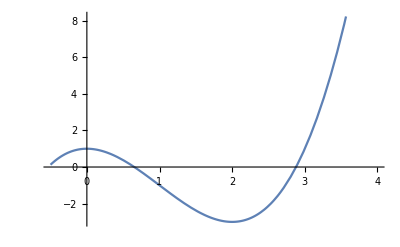

-6 x+3 x^2

{{x→0},{x→2}}

0

2

1

-3

3/8

17

```mathematica
Clear[x]
Clear[f]
Clear[fPrime]
f[x_]=x^3-3 x^2+1
Plot[f[x],{x,-1/2,4}]
fPrime[x_]=Dt[f[x],x]
criticalN=Solve[fPrime[x]==0,x]
criticalN[[1,1,2]]
criticalN[[2,1,2]]
f[criticalN[[1,1,2]]]
f[criticalN[[2,1,2]]]
f[1/2]
f[4]
```

3.2 THE MEAN VALUE THEOREM

## ROLLE’S THEOREM

### -Graphics-

### -Graphics-

### -Graphics-

## EXAMPLE 1

### -Graphics-

## EXAMPLE 2

### -Graphics-

### -Graphics-

-1+x+x^3

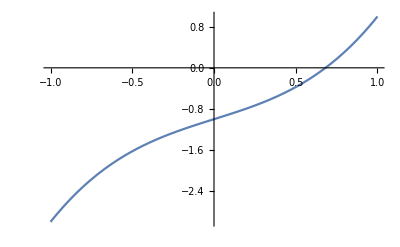

{{x→-0.341164-1.16154 ⅈ},{x→-0.341164+1.16154 ⅈ},{x→0.682328}}

```mathematica
Clear[f]
Clear [x]
f[x_]=x^3+x-1
Plot[f[x],{x,-1,1}]
NSolve[f[x]==0,x]
```

## THE MEAN VALUE THEOREM

### -Graphics-

### -Graphics--Graphics-

### -Graphics- -Graphics-

## EXAMPLE 3

### -Graphics-

-x+x^3

0

6

3

-1+3 x^2

{{x→-2/(√3)},{x→2/(√3)}}

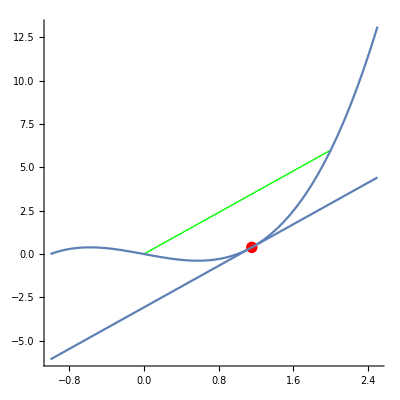

```mathematica
Clear[f]
Clear[x]
f[x_]=x^3-x
f[0]
f[2]
fprimec=(f[2]-f[0])/(2-0)
fprime[x_]=Dt[f[x],x]
Solve[fprime[x]==fprimec,x]
Show[Graphics[{Thick,Green,Line[{{0,0},{2,6}}]},Axes->True,AspectRatio->1],
Plot[f[x],{x,-1,2.5}],
ListPlot[{{2/(√3),f[2/(√3)]}},PlotStyle->{Red,PointSize[.02]}],
Plot[f[2/(√3)]+3(x-2/(√3)),{x,-1,2.5}]]
```

## EXAMPLE 4

### -Graphics-

## EXAMPLE 5

### -Graphics-

## THEOREM 5

### -Graphics-

## COROLLARY 7

### -Graphics-

3.3 DERIVATIVES AND THE SHAPES OF GRAPHS

## WHAT DOES f' SAY ABOUT f

### INCREASING / DECREASING TEST

#### -Graphics-

#### -Graphics-

### EXAMPLE 1

#### -Graphics-

5-12 x^2-4 x^3+3 x^4

-24 x-12 x^2+12 x^3

{{x→-1},{x→0},{x→2}}

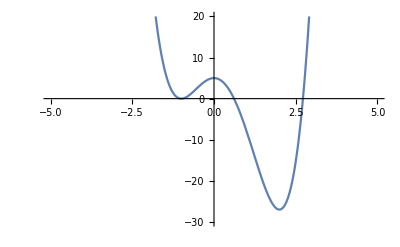

7.5

-13.5

```mathematica
Clear[f]
Clear [x]
Clear[fPrime]
f[x_]=3 x^4-4 x^3-12 x^2+5
fPrime[x_]=Dt[f[x],x]
Solve[fPrime[x]==0,x]
Plot[f[x],{x,-5,5},PlotRange->{{-30,20}}]
fPrime[-0.5]
fPrime[0.5]
```

### THE FIRST DERIVATIVE TEST

#### -Graphics-

#### -Graphics-

### EXAMPLE 2

#### -Graphics-

#### -Graphics-

```mathematica
Clear[f]
Clear [x]
Clear[fPrime]
f[x_]=3 x^4-4 x^3-12 x^2+5
fPrime[x_]=Dt[f[x],x]
Solve[fPrime[x]==0,x]
Plot[f[x],{x,-5,5},PlotRange->{{-30,20}}]
fPrime[-0.5]
fPrime[0.5]
```

5-12 x^2-4 x^3+3 x^4

-24 x-12 x^2+12 x^3

{{x→-1},{x→0},{x→2}}

-Graphics-

7.5

-13.5

### EXAMPLE 3

#### -Graphics-

#### -Graphics- -Graphics--Graphics-

x+2 Sin[x]

1+2 Cos[x]

{{x→(2 π)/3},{x→(4 π)/3}}

{{x→2.0944},{x→4.18879}}

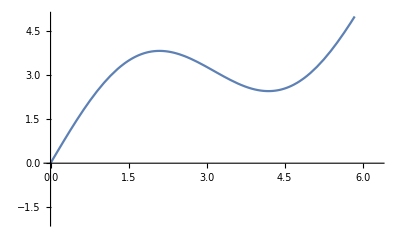

√3+(2 π)/3

-√3+(4 π)/3

3.82645

2.45674

```mathematica
Clear[g]
Clear [x]
Clear[gPrime]
g[x_]=x+2Sin[x]
gPrime[x_]=Dt[g[x],x]
Solve[gPrime[x]==0 && x≥0 && x≤2Pi,x]
NSolve[gPrime[x]==0 && x≥0 && x≤2Pi,x]
Plot[g[x],{x,0,2Pi},PlotRange->{{-2,5}}]
g[(2Pi)/3]
g[(4Pi)/3]
N[g[(2Pi)/3]]
N[g[(4Pi)/3]]
```

## WHAT DOES f'' SAY ABOUT f

### CONCAVE UPWARD AND CONCADE DOWNWARD ON (a, b)

#### -Graphics-

#### -Graphics--Graphics- -Graphics-

### DEFINITION: INFLECTION POINT

#### -Graphics-

### CONCAVITY TEST

#### -Graphics-

#### -Graphics-

### THE SECOND DERIVATIVE TEST

#### -Graphics-

#### -Graphics--Graphics- -Graphics-

### EXAMPLE 5

#### -Graphics-

-4 x^3+x^4

-12 x^2+4 x^3

-24 x+12 x^2

{{x→0},{x→0},{x→3}}

{{x→0},{x→2}}

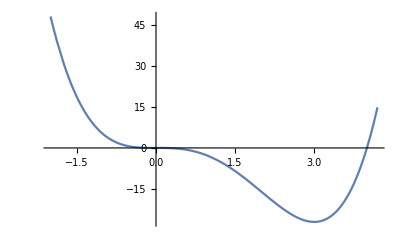

```mathematica
Clear[f,fp,fpp]
f[x_]=x^4-4 x^3
fp[x_]=Dt[f[x],x]
fpp[x_]=Dt[fp[x],x]
Solve[fp[x]==0,x]
Solve[fpp[x]==0,x]
Plot[f[x],{x,-2,4.2}]
```

### EXAMPLE 6

#### -Graphics-

(6-x)^(1/3) x^(2/3)

(2 (6-x)^(1/3))/(3 x^(1/3))-x^(2/3)/(3 (6-x)^(2/3))

-8/((6-x)^(5/3) x^(4/3))

{{x→4}}

{}

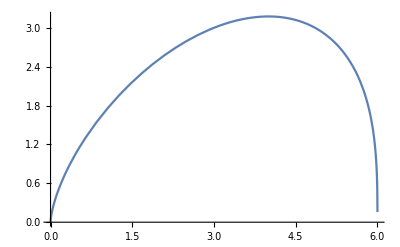

```mathematica
Clear[f,fp,fpp]
f[x_]=x^(2/3)*(6-x)^(1/3)
fp[x_]=Dt[f[x],x]
fpp[x_]=Dt[fp[x],x]//FullSimplify
Solve[fp[x]==0,x]
Solve[fpp[x]==0,x]
Plot[f[x],{x,-2,8},PlotRange->All]
```

3.4 CURVE SKETCHING

## GUIDELINES FOR SKETCHING A CURVE

### A. Domain

#### -Graphics-

### B. Intercepts

#### -Graphics-

### C. Symmetry

#### Even Function

-Graphics--Graphics-

#### Odd Fuction

-Graphics--Graphics-

#### Periodic function

-Graphics--Graphics-

### D. Asymptotes

#### (i) Horizontal Asymptotes

-Graphics-

#### (ii) Vertical Asymptotes

-Graphics-

#### Periodic function

-Graphics--Graphics-

### E. Intervals of Increase or Decrease

#### -Graphics-

### F. Local Maximum and Minimum

#### -Graphics-

### G. Concavity and Points of Inflection

#### -Graphics-

### H. Sketch the Curve

#### -Graphics-

### EXAMPLE 1

#### -Graphics-

(2 x^2)/(-1+x^2)

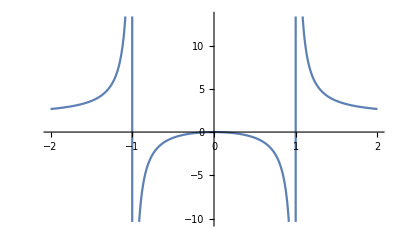

```mathematica
Clear[f]
f[x_]=(2 x^2)/(x^2-1)
Plot[f[x],{x,-2,2}]
```

### EXAMPLE 2

#### -Graphics-

x^2/(√(1+x))

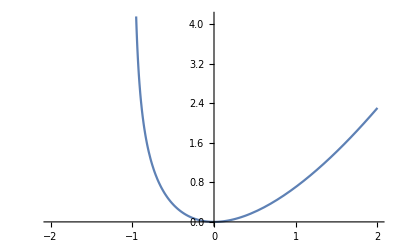

```mathematica
Clear[f]
f[x_]=x^2/(√(x+1))
Plot[f[x],{x,-2,2}]
```

### EXAMPLE 3

#### -Graphics-

Cos[x]/(2+Sin[x])

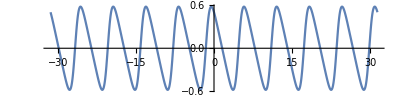

```mathematica
Clear[f]
f[x_]=Cos[x]/(2+Sin[x])
Plot[f[x],{x,-10Pi,10Pi},AspectRatio->1/4]
```

## GRAPHING WITH TECHNOLOGY

### EXAMPLE 4

#### -Graphics-

-2 x^2+3 x^3+3 x^5+2 x^6

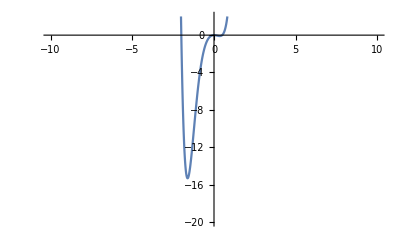

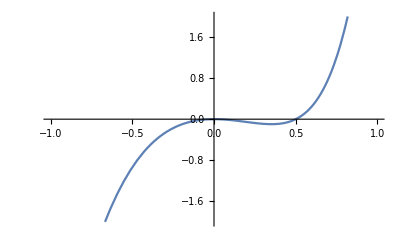

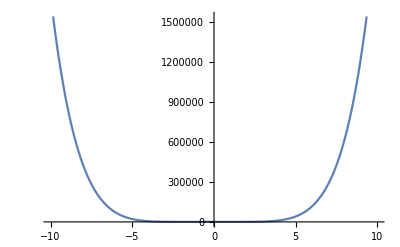

-4 x+9 x^2+15 x^4+12 x^5

-4+18 x+60 x^3+60 x^4

{{x→-1.61612},{x→0.},{x→0.00725417-0.765861 ⅈ},{x→0.00725417+0.765861 ⅈ},{x→0.351613}}

{{x→-1.23293},{x→0.0197473-0.528347 ⅈ},{x→0.0197473+0.528347 ⅈ},{x→0.193431}}

-15.3265

0

-0.0969495

```mathematica
Clear[f,fp,fpp]
f[x_]=2 x^6+3 x^5+3 x^3-2 x^2
Plot[f[x],{x,-10,10},PlotRange->{-20,2}]
Plot[f[x],{x,-1,1},PlotRange->{-2,2}]
Plot[f[x],{x,-10,10}]
fp[x_]=Dt[f[x],x]
fpp[x_]=Dt[fp[x],x]
NSolve[fp[x]==0,x]
NSolve[fpp[x]==0,x]
f[-1.616121794379201]
f[0]
f[0.35161346393335313]
```